# 1. Matrix-Vector Multiplication

We need to know how to get computers to build matrices and vectors and do all sorts of things to them.  Our matrices will mostly be real.

## Defining Matrices and Vectors

Random matrices are easy

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},n]
```

Typing in all the entries is a pain.

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}};
b={11,12,13};
```

Importing things from the web (or anywhere else) is easy.

SparseArray[…]

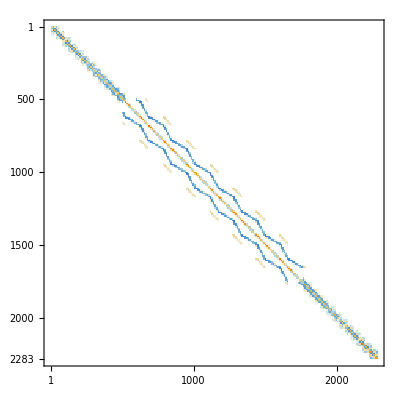

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/fidap/fidap024.mtx.gz"]
MatrixPlot[A]
```

If the file is on your computer the “File Path” file browser under Insert is convenient.  You can also set a directory using “SetDirectory”

## Getting Bits of matrices

Matrix entries are easy: double square brackets

```mathematica
A[[1,2]]
```

0.0866137

Rows or columns use a span notation

```mathematica
b=A⟦2,1;;10⟧
b=Normal[b]
```

SparseArray[…]

{-0.0236955,9.09382,0.00295465,-4.4734,0.,0.,0.,0.,0.,0.}

The “SparseArray” does not store the zeros.  The “Normal” vector does!

Sub matrices use the span notation twice! Matrices display flat. To get a pretty matrix use “MatrixForm”. 
You can NOT compute with the pretty version!

```mathematica
ASub=Normal[A⟦1;;4,1;;10⟧];
MatrixForm[ASub]
```

(9.00319 | 0.0866137 | -4.46207 | -0.0108505 | 0. | 0. | 0. | 0. | 0. | 0.
-0.0236955 | 9.09382 | 0.00295465 | -4.4734 | 0. | 0. | 0. | 0. | 0. | 0.
-4.46215 | -0.0108505 | 7.91508 | -0.0108944 | -4.49112 | 0. | 0.55762 | 0. | 0. | 0.
0.00295465 | -4.47348 | 0.0029472 | 7.90374 | 0. | -4.49112 | 0. | 0.55762 | 0. | 0.)

## Multiplying Matrices and Vectors

In Mathematica a dot means matrix-vector and matrix-matrix multiplication

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},n];
A.b
```

{0.603156,-0.422087,-0.228253,-0.39482,-0.462529,1.19036}

You get a warning if dimensions do not match!

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},m];
A.b
```

Dot::dotsh: Tensors {{0.565072,0.0371225,0.453954,-0.763316,0.222334},«4»,{-0.929396,0.884264,-«19»,-0.068005,0.244477}} and {0.303227,-0.967513,-0.137561,0.082273,0.286764,0.0227827} have incompatible shapes.

{{0.565072,0.0371225,0.453954,-0.763316,0.222334},{0.93624,0.314642,0.992573,-0.151933,0.848713},{-0.942118,0.536201,0.697918,-0.43491,-0.815213},{-0.0534818,0.335099,0.878368,-0.207077,0.167766},{-0.348248,-0.99451,0.215286,-0.558649,-0.687142},{-0.929396,0.884264,-0.636419,-0.068005,0.244477}}.{0.303227,-0.967513,-0.137561,0.082273,0.286764,0.0227827}

It works the same for matrix-matrix multiplication

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Dimensions[A.B]
```

{6,12}

## Multiplying Matrices from scratch: Efficiency!

You can define matrix-matrix multiplication C=A.B from C_(i,j)=∑_k A_(i,k)B_(k,j) if you want but it is going to be slower (in every way you can imagine) than the built in command!

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
CBuiltIn=A.B;
CFormula=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,n}],
{i,m},{j,r}];
Norm[CBuiltIn-CFormula]
```

0.

We can race the two versions!

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Timing[CBuiltIn=A.B;]
Timing[CFormula=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,n}],
{i,m},{j,r}];]
Norm[CBuiltIn-CFormula]
```

{0.,Null}

{0.,Null}

0.

## Assembling/Disassembling Matrices

We will frequently want to disassemble matrices and/or build matrices out of other matrices or vectors! For example, in the book we think of A is a bunch columns
	A=[a_1|a_2|…|a_n]

```mathematica
{m,n}={3,4};
A=RandomReal[{-1,1},{m,n}];
MatrixForm[A]
A⟦All,1⟧
A⟦1,All⟧
```

The book encourages us to think of 
	C=A.B=[A.b_1|A.b_2|…]
We can check this as follows

```mathematica
{m,n,r}={3,2,4};
A=RandomReal[{-1,1},{m,n}];B=RandomReal[{-1,1},{n,r}];
CBuiltIn=A.B;
CCols=Table[A.B⟦All,j⟧,{j,r}]ᵀ;
Map[MatrixForm,{CBuiltIn,CCols}]
```

{(-0.589144 | 0.599273 | -1.07051 | -0.0658416
-0.0495212 | -0.508266 | 0.107319 | -0.516374
-0.316431 | -0.133337 | -0.414201 | -0.451623),(-0.589144 | 0.599273 | -1.07051 | -0.0658416
-0.0495212 | -0.508266 | 0.107319 | -0.516374
-0.316431 | -0.133337 | -0.414201 | -0.451623)}

We can race the two versions!

```mathematica
{m,n,r}={3,122,4};
A=RandomReal[{-1,1},{m,n}];B=RandomReal[{-1,1},{n,r}];
Timing[CBuiltIn=A.B;]
Timing[CCols=Table[A.B⟦All,j⟧,{j,r}]ᵀ;]
Norm[CBuiltIn-CCols]
```

{0.,Null}

{0.,Null}

2.60698×10^-15

## Block Matrices and Blocks of Matrices

A block matrix 
	A=(A_11 | A_12
A_21 | A_22
A_31 | A_33)
simply slams matrices (of matching dimensions) together.

```mathematica
{m,n}={2,3};
{{A11,A12},
{A21,A22},
{A31,A32}}=RandomReal[{-1,1},{3,2,m,n}];
A=ArrayFlatten[{{A11,A12},{A21,A22},{A31,A32}}];
Dimensions[A];
Map[MatrixForm,{A,A31}]
```

{(-0.103366 | -0.0560508 | -0.673246 | 0.628678 | -0.830013 | 0.471258
-0.000253668 | -0.386386 | -0.371101 | 0.695964 | 0.866385 | -0.622134
0.354908 | 0.107301 | -0.994508 | 0.210882 | 0.0453324 | 0.918908
0.33374 | -0.470798 | -0.338157 | -0.497049 | -0.199733 | -0.39632
-0.747119 | -0.142282 | -0.0780345 | -0.669879 | -0.0559918 | 0.387909
0.410438 | -0.765385 | 0.0559693 | -0.770634 | 0.762139 | -0.92563),(-0.747119 | -0.142282 | -0.0780345
0.410438 | -0.765385 | 0.0559693)}

You can grab a chunk of a matrix using the range notation

```mathematica
Map[MatrixForm,{A[[1;;m,1;;n]],A11}]
```

{(-0.103366 | -0.0560508 | -0.673246
-0.000253668 | -0.386386 | -0.371101),(-0.103366 | -0.0560508 | -0.673246
-0.000253668 | -0.386386 | -0.371101)}

## Inverse Matrices and Linear Solves

Almost all random square matrices A have an inverse A^-1 satisfying A^-1.A=Id

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];
AInv=Inverse[A];
Norm[A.AInv-IdentityMatrix[m]]
```

1.16487×10^-15

Most of the time you do not want the inverse! You just want to solve the system A.x=b

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
Timing[AInv=Inverse[A]; bSlow=AInv.b;]
Timing[bFast=LinearSolve[A,b];]
Norm[bSlow-bFast]
```

{0.,Null}

{0.,Null}

2.7055×10^-16